```mathematica
Solve[{(1+q1)/ϵ1== q2/ϵ2, q1+q2==1},{q1,q2}]
```

{{q1→-(-ϵ1+ϵ2)/(ϵ1+ϵ2),q2→(2 ϵ2)/(ϵ1+ϵ2)}}

```mathematica
Clear[V, e1, e2]
```

```mathematica
V[r1_,r2_, ϵ1_, ϵ2_] := (2ϵ1)/(ϵ1+ϵ2) -1/(ϵ1 (r1+r2)) + (ϵ2-ϵ1)/(ϵ1+ϵ2) 1/(2 ϵ2 r2)
```

```mathematica
resnoimage=Simplify[Solve[D[V[5 ,r2,  3.5/(27.21*0.529),3.5/(27.21*0.529)]-F(5+r2),r2]==0 /.( r2-> r),r]]
```

{{r→-5.-2.02795/(√F)},{r→-5.+2.02795/(√F)}}

```mathematica
resnoimage/. F-> 0.001
resnoimage/. F-> 0.005
```

{{r→-69.1295},{r→59.1295}}

{{r→-33.6796},{r→23.6796}}

```mathematica
resimage= Simplify[Solve[D[V[5 ,r2,  1.0/(27.21*0.529),4.0/(27.21*0.529)]-0.001(5+r2),r2]==0 /.( r2-> r),r]]
resimage= Simplify[Solve[D[V[5,r2,  1.0/(27.21*0.529),4.0/(27.21*0.529)]-0.005(5+r2),r2]==0 /.( r2-> r),r]]
```

{{r→-74.4138},{r→-1.51196},{r→3.86523},{r→62.0606}}

{{r→-36.4762},{r→-1.51644},{r→4.08106},{r→23.9116}}

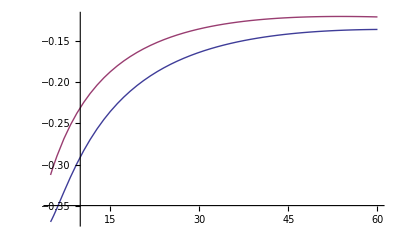

```mathematica
Plot[{ V[5,r2,  1./(27.21*0.529), 4.0/(27.21*0.529)]-0.001(5+r2),
 V[5,r2+2,  3.5/(27.21*0.529), 4.0/(27.21*0.529)]-0.001(5+r2)},{r2,5,60}]
```

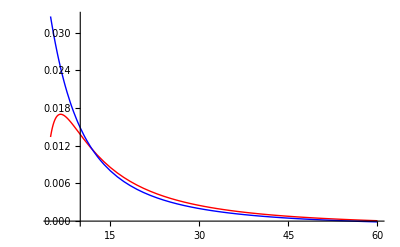

```mathematica
Plot[{D[ V[5 ,r2,  1./(27.21*0.529), 4.0/(27.21*0.529)]-0.001(5+r2),r2]/. {r2-> r},{D[ V[5 ,r2,  3.5/(27.21*0.529), 4.0/(27.21*0.529)]-0.001(5+r2),r2]/. {r2-> r}}},
{r,5,60}, PlotStyle-> {Red, Blue, Green}, PlotRange-> Full]
```

```mathematica
V[3,4,  3./(27.21*0.529), 4./(27.21*0.529)]
V[3,3,  3./(27.21*0.529), 4./(27.21*0.529)]
V[4,3,  3./(27.21*0.529), 4./(27.21*0.529)]
V[3,3,  3./(27.21*0.529), 4./(27.21*0.529)]
```

-0.612504

-0.699713

-0.587514

-0.699713

what about an interface dipole?

```mathematica
Clear[NRG]
NRG[x_] := (- 27.21 0.529)/(ϵ x)+ (μ 27.21 0.529^2)/(ϵ (x-5)^2) +F x
NRG[x_, r_] := (- 27.21 0.529)/(ϵ √(r^2+x^2))+ (μ 27.21 0.529^2 (x-5))/(ϵ ((x-5)^2)^(3/2)) +F x
```

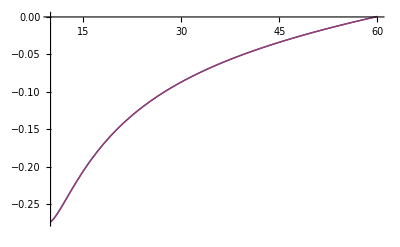

```mathematica
Plot[{NRG[x,0] /. {ϵ -> 4 , μ -> 1, F-> 0.001},NRG[x] /. {ϵ -> 4 , μ -> 1, F-> 0.001}}, {x,10,60}]
```

```mathematica
Plot3D[{NRG[x,r]/. {ϵ -> 4 , μ -> 1, F-> 0.001},NRG[x,r]/. {ϵ -> 4 , μ -> 1, F-> 0.001},NRG[x,r]/. {ϵ -> 4 , μ -> 0, F-> 0.00}},{x, 10,40},{r,0,30}, PlotRange-> All]
```

-Graphics3D-

```mathematica
Solve[(D[NRG[x, r],x]/.x->z)==0, z]
```

$Aborted

```mathematica
Solve[(D[NRG[x, 0] /.{ϵ-> 4, μ-> 1},x]/.{x->z})==0,z]
```

$Aborted